```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/fp/Desktop/Versuch 1.12

```mathematica
Data=Import["TestV.csv","Data","HeaderLines"->1]
```

{{1,1,0,89.837,173.162,0,1.076,1.752,3.784,9.124,23.897,36.384},{2,1,1,90.58,175.268,0,1.594,1.652,3.363,7.595,18.537,41.868},108674,{108677,9229,1844,389.475,621.923,0,0.79,1.958,4.697,12.571,36.38,137.577}}
 |  |  |  |

```mathematica
Data[[1]]
```

{1,1,0,89.837,173.162,0,1.076,1.752,3.784,9.124,23.897,36.384}

```mathematica
Traj=GatherBy[Data,#[[2]]&];
```

```mathematica
Traj[[1]];
```

```mathematica
Len=Length/@Traj;
```

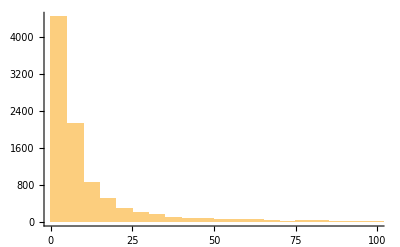

```mathematica
Histogram[Len,100,PlotRange->{{0,100},All}]
```

```mathematica
LenLong=Flatten[Position[Len,_?(#≥50&)]];
```

```mathematica
TrajLong=Traj[[LenLong]];
```

```mathematica
Diffs=Differences/@TrajLong
```

{{{1,0,1,0.743,2.106,0,0.518,-0.1,-0.421,-1.529,-5.36,5.484},131,{1,0,2,-2.822,4,-0.02,-0.262,-1.635,62.667}},390,{1}}
 |  |  |  |

```mathematica
Diffs[[1]];
```

```mathematica
Kx=Kurtosis[#[[All,4]]]&/@Diffs;
Ky=Kurtosis[#[[All,5]]]&/@Diffs;
```

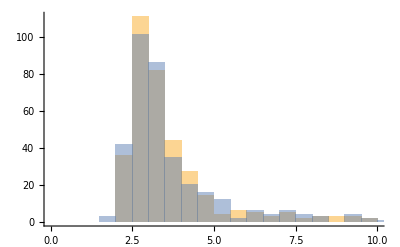

```mathematica
Histogram[{Kx,Ky},300,PlotRange->{{0,10},All}]
```

```mathematica
KKx=Flatten[Position[Kx,_?(#≤6&)]];
KKy=Flatten[Position[Ky,_?(#≤6&)]];
```

```mathematica
Kxy=Intersection[KKx,KKy];
```

```mathematica
DiffEnd=Diffs[[Kxy]];
```

```mathematica
DiffEnd[[1]];
```

```mathematica
Num=Length@DiffEnd
```

299

```mathematica
Lenn=Length/@TrajLong;
```

```mathematica
Long=Flatten[Position[Lenn,_?(#==Max[Lenn]&)]]
```

{232}

```mathematica
Xlong=#[[All,4]]&@TrajLong[[232]];
Ylong=#[[All,5]]&@TrajLong[[232]];
```

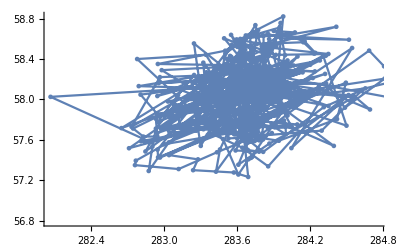

```mathematica
Show[ListLinePlot[Transpose[{Xlong,Ylong}]],ListPlot[Transpose[{Xlong,Ylong}]]]
```

```mathematica
Γx=Flatten[Standardize[#[[All,4]]]&/@DiffEnd];
Γy=Flatten[Standardize[#[[All,5]]]&/@DiffEnd];
```

```mathematica
Gx=Flatten[(#[[All,4]]-Mean[#[[All,4]]])/StandardDeviation[#[[All,4]]]&/@DiffEnd];
```

```mathematica
Skewness[Γx]
Skewness[Γy]
```

-0.0484392

0.0126785

```mathematica
Kurtosis[Γx]
Kurtosis[Γy]
```

3.25635

3.18898

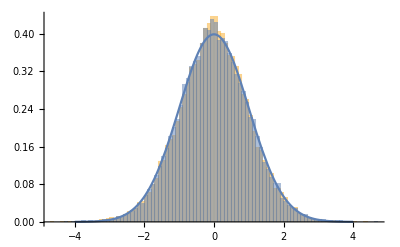

```mathematica
Show[Histogram[{Γx,Γy},100,"PDF"],Plot[PDF[NormalDistribution[],x],{x,-4,4}]]
```

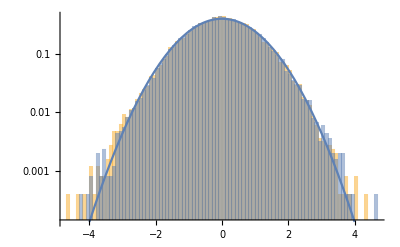

```mathematica
Show[Histogram[{Γx,Γy},100,"PDF",ScalingFunctions->"Log"],Plot[PDF[NormalDistribution[],x],{x,-4,4},ScalingFunctions->"Log"]]
```

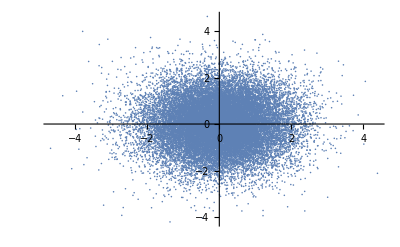

```mathematica
ListPlot[Transpose[{Γx,Γy}]]
```

```mathematica
qrank[x_]:=(Ordering@Ordering@x-0.5)/Length@x;
```

```mathematica
Qx=qrank[Γx];
Qy=qrank[Γy];
```

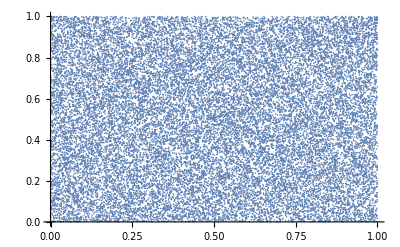

```mathematica
ListPlot[Transpose[{Qx,Qy}]]
```

```mathematica
Histogram3D[Transpose[{Qx,Qy}]]
```

-Graphics3D-

```mathematica
dx=Differences@Xlong;
dy=Differences@Ylong;
```

```mathematica
AutX=Table[Correlation[Drop[dx,-k],Drop[dx,k]],{k,0,Length[dx]-150}];
AutY=Table[Correlation[Drop[dy,-k],Drop[dy,k]],{k,0,Length[dy]-150}];
```

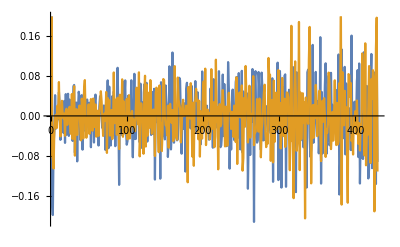

```mathematica
ListLinePlot[{AutX,AutY}]
```

```mathematica
AutX2=Table[Correlation[Drop[dx^2,-k],Drop[dx^2,k]],{k,0,Length[dx]-150}];
AutY2=Table[Correlation[Drop[dy^2,-k],Drop[dy^2,k]],{k,0,Length[dy]-150}];
```

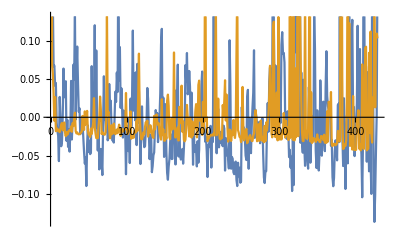

```mathematica
ListLinePlot[{AutX2,AutY2}]
```

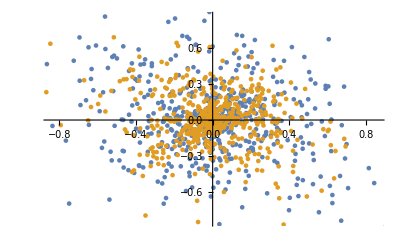

```mathematica
ListPlot[{Transpose[{Drop[dx,1],Drop[dx,-1]}],Transpose[{Drop[dy,1],Drop[dy,-1]}]}]
```

```mathematica
QDxv=qrank[Drop[dx,1]];
QDXh=qrank[Drop[dx,-1]];
```

```mathematica
Histogram3D[Transpose[{QDxv,QDXh}]]
```

-Graphics3D-